```mathematica
2+3
```

5

```mathematica
a={{6,1,1},{4,-2,5},{2,8,7}}
```

{{6,1,1},{4,-2,5},{2,8,7}}

```mathematica
a //MatrixForm
```

(6 | 1 | 1
4 | -2 | 5
2 | 8 | 7)

```mathematica
Det[a]
```

-306

```mathematica
MatrixRank[a]
```

3

```mathematica
Tr[a]
```

11

```mathematica
Inverse[a] //MatrixForm
```

(3/17 | -1/306 | -7/306
1/17 | -20/153 | 13/153
-2/17 | 23/153 | 8/153)

```mathematica
MatrixPower[a,3] //MatrixForm
```

(336 | 162 | 228
406 | 162 | 469
698 | 702 | 905)

```mathematica
b = {{2,37,71}, {4,5,7}, {9,8,19}}
```

{{2,37,71},{4,5,7},{9,8,19}}

```mathematica
b //MatrixForm
```

(2 | 37 | 71
4 | 5 | 7
9 | 8 | 19)

```mathematica
Print["Determinant = ", Det[b]]
```

Determinant = -1326

```mathematica
Print["trace = ",Tr[b] ]
```

trace = 26

```mathematica
Print["Inverse Matrix: ", Inverse[b]//MatrixForm]
```

Inverse Matrix: (-1/34 | 45/442 | 16/221
1/102 | 601/1326 | -45/221
1/102 | -317/1326 | 23/221)

```mathematica
Print["Rank Matrix: ", MatrixRank[b]]
```

```mathematica
"Inverse Matrix: "3
```

```mathematica
Print["Matrix Power: ", MatrixPower[b,3]//MatrixForm]
```

Matrix Power: (20640 | 47402 | 95200
5166 | 8128 | 16652
12046 | 19250 | 39430)

```mathematica
Print[b . Inverse[b]//MatrixForm]
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
{c,d} = Eigensystem[b]
```

{{,,},{{,,1},{,,1},{,,1}}}

```mathematica
Print[c//MatrixForm]
```

(

)

```mathematica
Print[d//MatrixForm]
```

( |  | 1
 |  | 1
 |  | 1)

```mathematica
DiagonalMatrix[{1,2,3}]
```

```mathematica
{{1,0,0},{0,2,0},{0,0,3}}
```

```mathematica
f[x_]:=Tan[x]+Exp[-(Sin[1/(1+x^2)])^2]
```

```mathematica
phi[x_]:=ArcTan[-Exp[-(Sin[1/(1+x^2)])^2]]
```

```mathematica
D[phi[x],x]
```

-(4 ⅇ^(-Sin[1/(1+x^2)]^2) x Cos[1/(1+x^2)] Sin[1/(1+x^2)])/((1+ⅇ^(-2 Sin[1/(1+x^2)]^2)) (1+x^2)^2)

```mathematica
phi'[0]
```

0

```mathematica
N[phi'[1]]
```

-0.204931

```mathematica
-(ⅇ^(-Sin[1/2]^2) Cos[1/2] Sin[1/2])/(1+ⅇ^(-2 Sin[1/2]^2))
```

```mathematica
NestList[phi,0.5, 10]
```

{0.5,-0.538756,-0.549812,-0.553007,-0.553932,-0.554201,-0.554279,-0.554301,-0.554308,-0.55431,-0.55431}

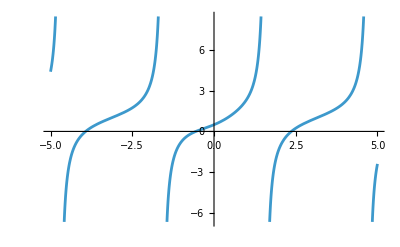

```mathematica
Plot[f[x],{x,-5,5}]
```

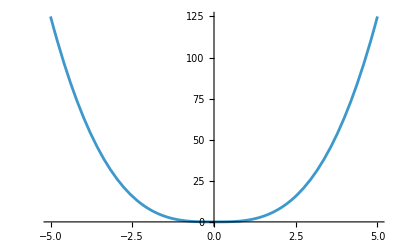

```mathematica
Plot[Abs[x]^3,{x,-5,5}]
```

```mathematica
Integrate[1/(x^2-5x+4),x]
```

-1/3 Log[1-x]+1/3 Log[4-x]

```mathematica
Integrate[Exp[x]*Cos[x],x]
```

1/2 ⅇ^x (Cos[x]+Sin[x])

```mathematica
Integrate[1/((5-x)*(1-x)^0.5),x]
```

-ArcTan[0.5 √(1.-1. x)]

```mathematica
Integrate[Sin[Log[x]],x]
```

```mathematica
-1/2 x Cos[Log[x]]+1/2 x Sin[Log[x]]
```

```mathematica
Integrate[((Sin[x])^3)/(2+Cos[x]),x]
```

-2 Cos[x]+1/4 Cos[2 x]+3 Log[2+Cos[x]]

```mathematica
Print[((Sin[x^3]))/(2+Cos[x])]
```

Sin[x^3]/(2+Cos[x])

```mathematica
A={{1,2,3,4,5},{6,7,8,9,10},{11,12,13,14,15}}
```

{{1,2,3,4,5},{6,7,8,9,10},{11,12,13,14,15}}

```mathematica
A//MatrixForm
```

(1 | 2 | 3 | 4 | 5
6 | 7 | 8 | 9 | 10
11 | 12 | 13 | 14 | 15)

```mathematica
A[[All,{3,4}]] //MatrixForm
```

(3 | 4
8 | 9
13 | 14)

```mathematica
B=A[[{1,2,3},{2,3,4}]]
```

{{2,3,4},{7,8,9},{12,13,14}}

```mathematica
C2=A[[1;;3,2;;4]]
```

{{2,3,4},{7,8,9},{12,13,14}}

```mathematica
B//MatrixForm
```

(2 | 3 | 4
7 | 8 | 9
12 | 13 | 14)

```mathematica
C2//MatrixForm
```

(2 | 3 | 4
7 | 8 | 9
12 | 13 | 14)